## Plotting representative trajectories

### Define the flow

```mathematica
flow = {x+y,y-x}
dynsys = {x'[t] == x[t]+y[t],y'[t]==y[t]-x[t]}
```

{x+y,-x+y}

{x'[t]==x[t]+y[t],y'[t]==-x[t]+y[t]}

### Make a stream plot

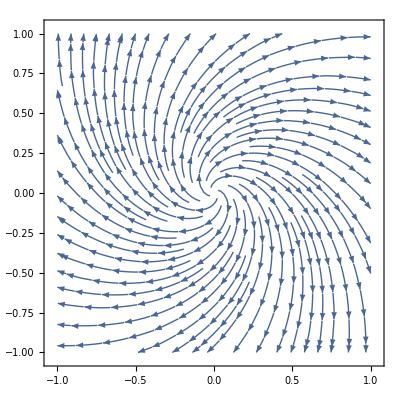

```mathematica
StreamPlot[flow,{x,-1,1},{y,-1,1}]
```

### Define function that generates trajectories

```mathematica
Join[dynsys,{x[0]==u,y[0]==v}]
```

{x'[t]==x[t]+y[t],y'[t]==-x[t]+y[t],x[0]==u,y[0]==v}

```mathematica
(* function that makes trajectories *)
sol[u_,v_,T_]:= NDSolve[Join[dynsys,{x[0]==u,y[0]==v}],{x[t],y[t]},{t,0,T}]//Flatten
```

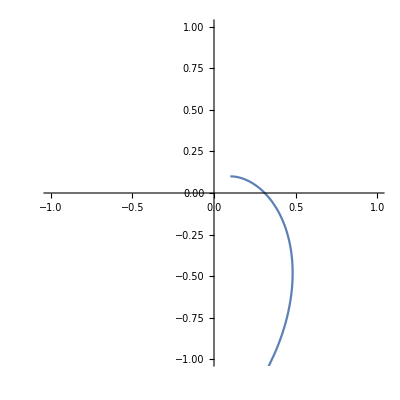

```mathematica
fullTime = 10;
{x[t],y[t]}/.sol[1,1,fullTime];
ParametricPlot[Evaluate[{x[t],y[t]}/.sol[.1,.1,fullTime]],{t,0,fullTime},PlotRange->{{-1,1},{-1,1}}]
```

### Generate list of trajetories

```mathematica
(* generate initial conditions on small circle *)
rcirc = 1;
npoints = 10;
sollist = Table[sol[rcirc Cos[θ],rcirc Sin[θ],fullTime],{θ,0,2 π,(2π)/npoints}];
ParametricPlot[Evaluate[{x[t],y[t]}/.sollist],{t,0,fullTime},PlotRange->{{-1,1},{-1,1}},PlotStyle->Blue];
```

### Fixed point is unstable? Invert time!

```mathematica
(* invert the time by letting flow -> -flow *)
flowinverted = {-x-y,-y+x}
dynsysinverted = {x'[t] == -x[t]-y[t],y'[t]==-y[t]+x[t]}
```

{-x-y,x-y}

{x'[t]==-x[t]-y[t],y'[t]==x[t]-y[t]}

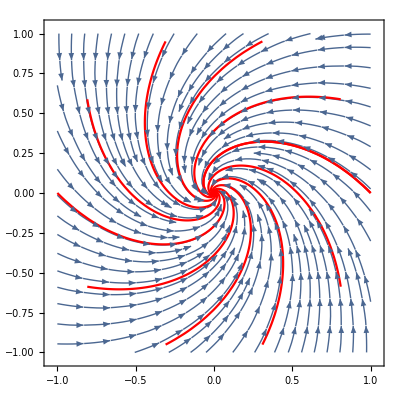

```mathematica
streamplot =StreamPlot[flowinverted,{x,-1,1},{y,-1,1}];
solinverted[u_,v_,T_]:= NDSolve[Join[dynsysinverted,{x[0]==u,y[0]==v}],{x[t],y[t]},{t,0,T}]//Flatten
sollistinverted = Table[solinverted[rcirc Cos[θ],rcirc Sin[θ],fullTime],{θ,0,2 π,(2π)/npoints}];
trajplot =ParametricPlot[Evaluate[{x[t],y[t]}/.sollistinverted],{t,0,fullTime},PlotRange->{{-1,1},{-1,1}},PlotStyle->Red];
Show[streamplot,trajplot]
```

## Example: Poincaré-Bendixon

### Define flow

```mathematica
xdot=x - y -x^3;
ydot =x + y -y^3;
flow={xdot,ydot}
(* calculate fixed points *)
fixsol=NSolve[flow==0,{x,y},Reals]
```

{x-x^3-y,x+y-y^3}

{{x→0.,y→0.}}

### Make StreamPlot

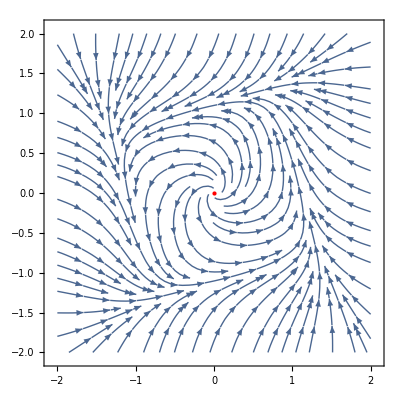

```mathematica
streamplot=Show[
StreamPlot[flow,{x,-2,2},{y,-2,2}],
Graphics[{PointSize[Large],Red,Point[{x,y}/.fixsol]}]
]
```

### Transform to polar coordinates

```mathematica
Solve[{rdot Cos[θ]-r Sin[θ]θdot,rdot Sin[θ]+r Cos[θ]θdot}==flow/.{x->r Cos[θ],y->r Sin[θ]},{rdot,θdot}]//Simplify//Flatten;
flowpol={rdot,θdot}/.% (* flow in polar coordinates *)
```

{-1/4 r (-4+3 r^2+r^2 Cos[4 θ]),1+1/4 r^2 Sin[4 θ]}

### Find conditions for fixed flow signs in radial direction

```mathematica
Reduce[flowpol[[1]]>0&&r>0&&0≤ θ<2π,r](* find condition for rdot>0 *)
Simplify[%,{θ==π/4}]
Reduce[flowpol[[1]]<0&&r>0&&0≤θ<2π,r](* find condition for rdot>0 *)
Simplify[%,{θ==0}]
```

0≤θ<2 π&&0<r<2 √(1/(3+Cos[4 θ]))

0<r<√2

0≤θ<2 π&&r>2 √(1/(3+Cos[4 θ]))

r>1

### Plot circles in StreamPlot

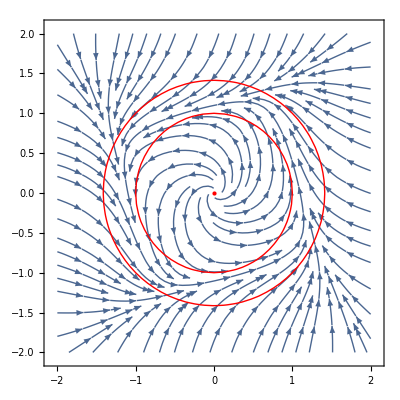

```mathematica
Show[
streamplot,
ContourPlot[x^2+y^2 ==2,{x,-2,2},{y,-2,2},ContourStyle->{Thick,Red}],
ContourPlot[x^2+y^2 ==1,{x,-2,2},{y,-2,2},ContourStyle->{Thick,Red}]
]
```

### Plot radial flow as function of θ

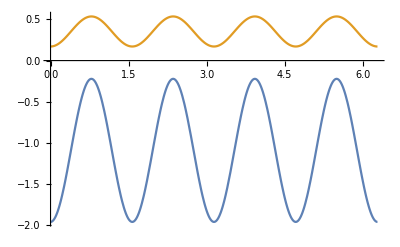

```mathematica
Plot[{flowpol[[1]]/.r->Sqrt[2]+0.1,flowpol[[1]]/.r->1-0.1},{θ,0,2π}]
```

## Other Stuff

```mathematica
(* how to use a rule *)
x/.{x-> a}
```

a

```mathematica
(* generate a list according to a certain rule *)
Table[n,{n,0,10,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
(* Simplifying an expression *)
Simplify[Sin[θ]^2 + Cos[θ]^2]
```

1

```mathematica
(* quitting the Kernel *)
Quit[]
```